Function[{probMismatch,probBetterWins},probMismatch probBetterWins (1-probBetterWins) 2+(1-probMismatch)/2]

Function[{probMismatch,probBetterWins},1-probDiff[probMismatch,probBetterWins]]

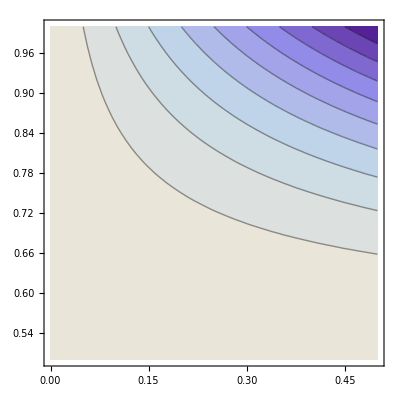

-Graphics3D-

Function[{probMismatch,probBetterWins,nS,nD},probSame[probMismatch,probBetterWins]^nS probDiff[probMismatch,probBetterWins]^nD]

4

6

0.00119439

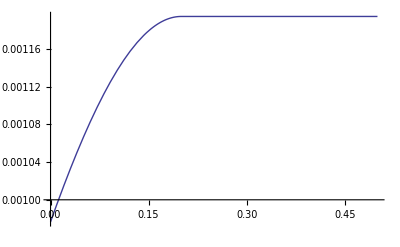

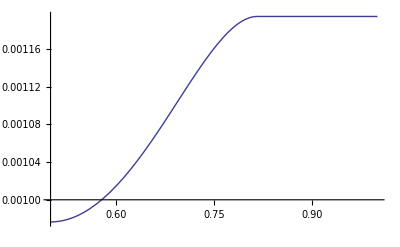

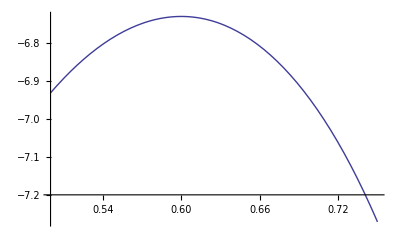

-Graphics3D-

```mathematica
probDiff = Function[{probMismatch, probBetterWins}, probMismatch probBetterWins(1-probBetterWins) 2  + (1 -probMismatch)/2]
probSame = Function[{probMismatch, probBetterWins}, 1 - probDiff[probMismatch, probBetterWins]]
ContourPlot[probDiff[m,b], {m, 0, 0.5}, {b,0.5,1}]
Plot3D[probSame[m,b], {m, 0, 0.5}, {b,0.5,1}]
LikelihoodTwo = Function[{probMismatch, probBetterWins, nS,nD}, (probSame[probMismatch, probBetterWins]^nS) (probDiff[probMismatch, probBetterWins]^nD)]
nDiff =4
nSame = 6
threshold2 = Log[LikelihoodTwo[(nSame - nDiff)/(nSame + nDiff),1,  nSame, nDiff]] -3;
ContourPlot[Log[LikelihoodTwo[m,b, nSame, nDiff]], {m, 0, .5}, {b,0.5,1}];
Plot3D[{Log[LikelihoodTwo[m,b,  nSame, nDiff]]}, {m, 0, .5}, {b,0.5,1}];


nS = nSame;
nD = nDiff;
pHat = (nSame)/(nSame+nDiff);
pMProfile = Function[{probMismatch}, If[nS < nD, LikelihoodTwo[probMismatch, 1, nS, nD], If[probMismatch < (nS-nD)/(nS + nD),  LikelihoodTwo[probMismatch, 1, nS, nD],LikelihoodTwo[probMismatch,(2 probMismatch + √(4 probMismatch probMismatch - 8 probMismatch (probMismatch/2 + .5 - pHat)))/(4 probMismatch) , nS, nD]]]];
pBProfile = Function[{probBetterWins}, If[nS < nD, LikelihoodTwo[0, probBetterWins, nS, nD], If[probSame[0.5,probBetterWins] <pHat,  LikelihoodTwo[0.5, probBetterWins, nS, nD],LikelihoodTwo[(pHat - .5)/(.5-2probBetterWins + 2 probBetterWins probBetterWins ), probBetterWins, nS, nD]]]];
pMProfile[.5]
Plot[pMProfile[m], {m, 0, .5}, PlotStyle->{Thick}]
Plot[pBProfile[b], {b, 0.5, 1}, PlotStyle->{Thick}]
Plot[nSame Log[p] + nDiff Log[1-p], {p,.5,.75}]
Plot3D[{threshold2, Log[LikelihoodTwo[m,b,  nSame, nDiff]]}, {m, 0, .5}, {b,0.5,1},PlotStyle->{{Red, Opacity[.5]},{}}]
```

```mathematica
Plot3D[{Log[LikelihoodTwo[m,b,  nSame, nDiff]], threshold2}, {m, 0, .5}, {b,0.5,1},PlotStyle->{{Blue},{Red, Opacity[.5]}}]
```

Plot3D::legacycolfunc: Use ColorFunction to specify coloring.

-Graphics3D-

1

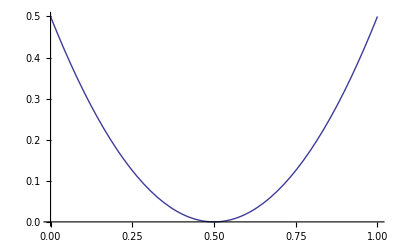

```mathematica
mi = 1
Plot[mi (.5-2w + 2w w ),{w,0,1}, PlotStyle->{Thick}]
```

```mathematica
(1 +.4^.5)/2
```

0.816228

```mathematica
testM = 0.5;
testB = 1;
probSame[testM, testB]
```

0.75

0.625

Function[{probMismatch,probBetterWins,nS,nD},probSame[probMismatch,probBetterWins]^nS probDiff[probMismatch,probBetterWins]^nD]

Function[{probMismatch,probBetterWins,nZ,nO},probZThree[probMismatch,probBetterWins]^nZ probOThree[probMismatch,probBetterWins]^nO]

Function[{probMismatch,probBetterWins,nS,nD,nZ,nO},LikelihoodTwo[probMismatch,probBetterWins,nS,nD] LikelihoodThree[probMismatch,probBetterWins,nZ,nO]]

400

600

400

600

-676.012

-676.012

-1349.02

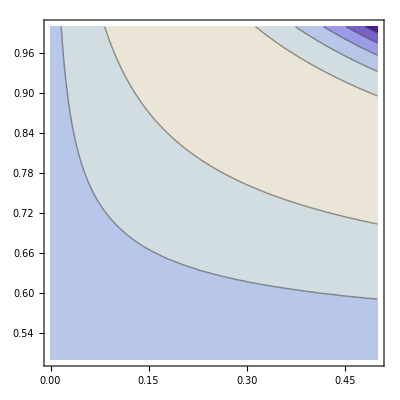

-Graphics3D-

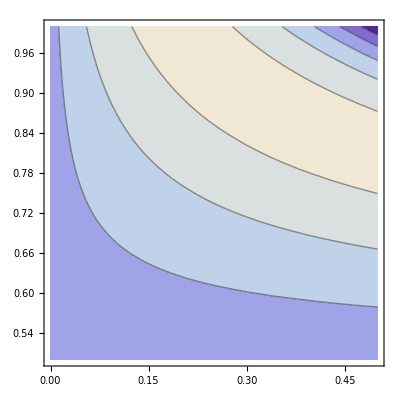

-Graphics3D-

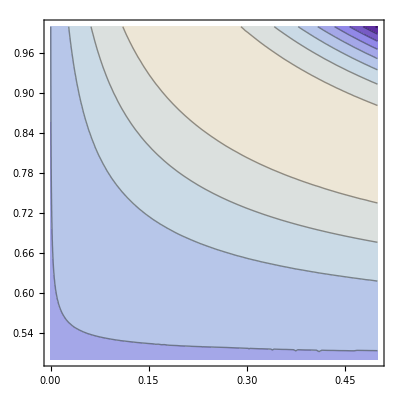

-Graphics3D-

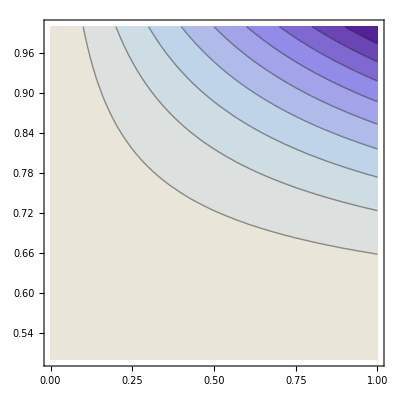

-Graphics3D-

```mathematica
LikelihoodTwo = Function[{probMismatch, probBetterWins, nS,nD}, (probSame[probMismatch, probBetterWins]^nS) (probDiff[probMismatch, probBetterWins]^nD)]
LikelihoodThree = Function[{probMismatch, probBetterWins, nZ,nO}, (probZThree[probMismatch, probBetterWins]^nZ) (probOThree[probMismatch, probBetterWins]^nO)]
Likelihood = Function[{probMismatch, probBetterWins, nS, nD, nZ,nO}, LikelihoodTwo[probMismatch, probBetterWins, nS, nD] LikelihoodThree[probMismatch, probBetterWins, nZ,nO]]
nDiff =4
nSame = 6
nZeroOfThree = 400
nOneOfThree = 600
threshold2 = Log[LikelihoodTwo[.2,1,  nSame, nDiff]] -3
threshold3 = Log[LikelihoodThree[.2,1,  nZeroOfThree, nOneOfThree]] -3
threshold = threshold2 + threshold3 + 3
ContourPlot[Log[LikelihoodTwo[m,b, nSame, nDiff]], {m, 0, .5}, {b,0.5,1}]
Plot3D[{Log[LikelihoodTwo[m,b,  nSame, nDiff]], threshold2}, {m, 0, .5}, {b,0.5,1},PlotStyle->{{},{Red, Opacity[.5]}}]
ContourPlot[Log[LikelihoodThree[m,b, nZeroOfThree, nOneOfThree]], {m, 0, .5}, {b,0.5,1}]
Plot3D[{Log[LikelihoodThree[m,b,  nZeroOfThree, nOneOfThree]], threshold3}, {m, 0, .5}, {b,0.5,1}, PlotStyle->{{},{Red, Opacity[.5]}}]
ContourPlot[Log[Likelihood[m,b,  nSame, nDiff, nZeroOfThree, nOneOfThree]], {m, 0, .5}, {b,0.5,1}]
Plot3D[{Log[Likelihood[m,b,  nSame, nDiff,  nZeroOfThree, nOneOfThree]], threshold}, {m, 0, .5}, {b,0.5,1}, PlotStyle->{{},{Red, Opacity[.5]}}]
```

```mathematica
nD =400
nS = 600
Solve[D[nD Log[probMismatch probBetterWins(1-probBetterWins) 2  + (1 -probMismatch)/2] + nS Log[1 - probMismatch probBetterWins(1-probBetterWins) 2  - (1 -probMismatch)/2], {probMismatch}] == 0, {probMismatch}]
Solve[D[nD Log[probMismatch probBetterWins(1-probBetterWins) 2  + (1 -probMismatch)/2] + nS Log[1 - probMismatch probBetterWins(1-probBetterWins) 2  - (1 -probMismatch)/2], {probBetterWins}
]== 0,{probBetterWins}]

Solve[D[nZeroOfThree  Log[probMismatch (probBetterWins^3 + (1-probBetterWins)^3)  + (1 -probMismatch)/4]    + nOneOfThree Log[1-probMismatch (probBetterWins^3 + (1-probBetterWins)^3)  + (1 -probMismatch)/4],{probMismatch}] == 0, {probMismatch}]
Solve[D[nZeroOfThree  Log[probMismatch (probBetterWins^3 + (1-probBetterWins)^3)  + (1 -probMismatch)/4]    + nOneOfThree Log[1-probMismatch (probBetterWins^3 + (1-probBetterWins)^3)  + (1 -probMismatch)/4],{probBetterWins}] == 0, {probBetterWins}]
```

400

600

{{probMismatch→1/(5 (-1+2 probBetterWins)^2)}}

{{probBetterWins→1/2},{probBetterWins→(-√5+5 √probMismatch)/(10 √probMismatch)},{probBetterWins→(√5+5 √probMismatch)/(10 √probMismatch)}}

{{probMismatch→(5-28 probBetterWins+28 probBetterWins^2)/(5 (-1+2 probBetterWins)^2 (5-12 probBetterWins+12 probBetterWins^2))}}

{{probBetterWins→1/2},{probBetterWins→(15 probMismatch-√15 √(7 probMismatch-4 probMismatch^2))/(30 probMismatch)},{probBetterWins→(15 probMismatch+√15 √(7 probMismatch-4 probMismatch^2))/(30 probMismatch)}}

Function[{probMismatch},If[nS<nD,Likelihood[probMismatch,1,nS,nD],If[probMismatch<(nS-nD)/(nS+nD),Likelihood[probMismatch,1,nS,nD],Likelihood[probMismatch,(-√5+5 √probMismatch)/(10 √probMismatch),nS,nD]]]]

Function[{probBetterWins},If[nS<nD,Likelihood[0,probBetterWins,nS,nD],If[probSame[0.5,probBetterWins]<nS/(nS+nD),Likelihood[0.5,probBetterWins,nS,nD],Likelihood[1/(5 (-1+2 probBetterWins)^2),probBetterWins,nS,nD]]]]

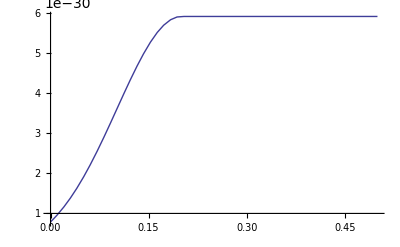

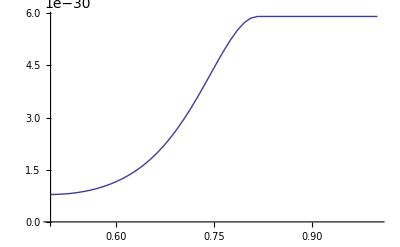

```mathematica
pMProfile = Function[{probMismatch}, If[nS < nD, Likelihood[probMismatch, 1, nS, nD], If[probMismatch < (nS-nD)/(nS + nD),  Likelihood[probMismatch, 1, nS, nD],Likelihood[probMismatch, (-√5+5 √probMismatch)/(10 √probMismatch), nS, nD]]]]
pBProfile = Function[{probBetterWins}, If[nS < nD, Likelihood[0, probBetterWins, nS, nD], If[probSame[0.5,probBetterWins] < nS/(nS + nD),  Likelihood[0.5, probBetterWins, nS, nD],Likelihood[1/(5 (-1+2 probBetterWins)^2), probBetterWins, nS, nD]]]]
Plot[pMProfile[m], {m, 0, .5}]
Plot[pBProfile[b], {b, 0.5, 1}]
```

```mathematica
probZThree = Function[{probMismatch, probBetterWins}, probMismatch (probBetterWins^3 + (1-probBetterWins)^3)  + (1 -probMismatch)/4]
probOThree = Function[{probMismatch, probBetterWins}, 1 - probZThree[probMismatch, probBetterWins]]
ContourPlot[probZThree[m,b], {m, 0.5, 1}, {b,0.5,1}]
Plot3D[probZThree[m,b], {m, 0.5, 1}, {b,0.5,1}]
```

```mathematica
probZThree[testM, testB]
```